## Define Models, Give Basic Example

```mathematica
(* Defining parameters *)
poppars={n1->500.,n2->500.};
PRpars = {PR1 -> 0.1, PR2->.05};
(* Aligning Movement parameters *)
tarpars= {ϕ1->1/5., τ12 ->1/3.,ϕ2->1/20.,τ21 ->1/3.};
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
RMpars = {a->.27,c->.15,g->.1,r->1/200.};
```

```mathematica
(* This is the TaR Ross-Macdonald Model *)
ψ ={{τ12/(τ12 + ϕ1),ϕ1/(τ12 + ϕ1)},{ϕ2/(τ21 + ϕ2),τ21/(τ12 + ϕ2)}};
Transpose[ψ].{n1,n2};
κ[PR1_,PR2_]:=  Transpose[ψ].{PR1*n1,PR2*n2}/Transpose[ψ].{n1,n2};
RTaR[PR1_,PR2_]:=Inverse[ψ].({PR1,PR2}/{(1-PR1),(1-PR2)})/(κ[PR1,PR2]/(1 + (a c)/g κ[PR1,PR2]))
```

```mathematica
(* First example of solving the TaR Ross-Macdonald Model *)
Inverse[ψ].({PR1,PR2}/{(1-PR1),(1-PR2)})/(κ[PR1,PR2]/(1 + (a c)/g κ[PR1,PR2]))/.PRpars/.tarpars/.RMpars/.poppars
```

{1.76437,0.58693}

```mathematica
RTaR[.1,.05]/.tarpars/.poppars/.RMpars
```

{1.76437,0.58693}

```mathematica
(* This is the Flux Model *)
RFlux[PR1_,PR2_]:=(r* {PR1,PR2}+({ f12*PR1 -f21*PR2 ,f21 PR2 - f12 PR1}))/{1-PR1, 1-PR2}/((r {PR1,PR2})/(1 +(a c)/g{PR1,PR2}))
```

```mathematica
(* First example of solving the Flux Ross-Macdonald Model *)
RFlux[PR1,PR2]/.PRpars/.fluxpars/.tarpars/.RMpars
```

{20.6341,-35.1134}

#### Test example : no travel

```mathematica
tarpars= {ϕ1->0., τ12 ->1/3.,ϕ2->0.,τ21 ->1/3.};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
```

```mathematica
RTaR[PR1,PR2]/.{PR1->.25,PR2->.25}/.tarpars/.poppars/.RMpars

-(g+a c PR1)/(g (-1+PR1))/.RMparams/.PR1->.25
```

{1.46833,1.46833}

ReplaceAll::reps: {RMparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(1.33333 (0.25 a c+g))/g/.RMparams

```mathematica
RFlux[PR1,PR2]/.{PR1->.25,PR2->.25}/.fluxpars/.tarpars/.poppars/.RMpars
```

{1.46833,1.46833}

#### Another example : travel, but with zero PR in one of the locations

```mathematica
tarpars= {ϕ1->1/1000., τ12 ->1/10.,ϕ2->1/10000.,τ21 ->1/10.};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
```

```mathematica
ψ/.tarpars
κ[PR1,PR2]/.{PR1->.25,PR2->0.02}/.tarpars/.poppars

fluxpars/.tarpars
```

{{0.990099,0.00990099},{0.000999001,0.999001}}

{0.249768,0.0222571}

{f12→0.00109,f21→0.00109}

```mathematica
Table[Flatten[{
X,
RTaR[PR1,PR2]/.{PR1->X,PR2->0.05}/.RMpars/.tarpars/.poppars,
-(g+a c PR1)/(g (-1+PR1))/.RMparams/.PR1->X
}],{X,0.01,.5,.01}]
```

ReplaceAll::reps: {RMparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{0.01,0.967561,1.08316,(1.0101 (0.01 a c+g))/g/.RMparams},{0.02,1.0109,1.08085,(1.02041 (0.02 a c+g))/g/.RMparams},{0.03,1.03544,1.07854,(1.03093 (0.03 a c+g))/g/.RMparams},{0.04,1.05549,1.07624,(1.04167 (0.04 a c+g))/g/.RMparams},{0.05,1.07395,1.07395,(1.05263 (0.05 a c+g))/g/.RMparams},{0.06,1.09177,1.07166,(1.06383 (0.06 a c+g))/g/.RMparams},{0.07,1.10939,1.06937,(1.07527 (0.07 a c+g))/g/.RMparams},{0.08,1.12702,1.06708,(1.08696 (0.08 a c+g))/g/.RMparams},{0.09,1.14478,1.0648,(1.0989 (0.09 a c+g))/g/.RMparams},{0.1,1.16277,1.06252,(1.11111 (0.1 a c+g))/g/.RMparams},{0.11,1.18102,1.06025,(1.1236 (0.11 a c+g))/g/.RMparams},{0.12,1.19959,1.05798,(1.13636 (0.12 a c+g))/g/.RMparams},{0.13,1.21851,1.05571,(1.14943 (0.13 a c+g))/g/.RMparams},{0.14,1.2378,1.05344,(1.16279 (0.14 a c+g))/g/.RMparams},{0.15,1.2575,1.05118,(1.17647 (0.15 a c+g))/g/.RMparams},{0.16,1.27763,1.04892,(1.19048 (0.16 a c+g))/g/.RMparams},{0.17,1.29821,1.04666,(1.20482 (0.17 a c+g))/g/.RMparams},{0.18,1.31927,1.0444,(1.21951 (0.18 a c+g))/g/.RMparams},{0.19,1.34082,1.04215,(1.23457 (0.19 a c+g))/g/.RMparams},{0.2,1.36288,1.03989,(1.25 (0.2 a c+g))/g/.RMparams},{0.21,1.38549,1.03763,(1.26582 (0.21 a c+g))/g/.RMparams},{0.22,1.40866,1.03538,(1.28205 (0.22 a c+g))/g/.RMparams},{0.23,1.43242,1.03313,(1.2987 (0.23 a c+g))/g/.RMparams},{0.24,1.45679,1.03087,(1.31579 (0.24 a c+g))/g/.RMparams},{0.25,1.4818,1.02862,(1.33333 (0.25 a c+g))/g/.RMparams},{0.26,1.50747,1.02636,(1.35135 (0.26 a c+g))/g/.RMparams},{0.27,1.53384,1.0241,(1.36986 (0.27 a c+g))/g/.RMparams},{0.28,1.56093,1.02184,(1.38889 (0.28 a c+g))/g/.RMparams},{0.29,1.58878,1.01958,(1.40845 (0.29 a c+g))/g/.RMparams},{0.3,1.61742,1.01732,(1.42857 (0.3 a c+g))/g/.RMparams},{0.31,1.64688,1.01505,(1.44928 (0.31 a c+g))/g/.RMparams},{0.32,1.67721,1.01278,(1.47059 (0.32 a c+g))/g/.RMparams},{0.33,1.70843,1.01051,(1.49254 (0.33 a c+g))/g/.RMparams},{0.34,1.7406,1.00823,(1.51515 (0.34 a c+g))/g/.RMparams},{0.35,1.77375,1.00595,(1.53846 (0.35 a c+g))/g/.RMparams},{0.36,1.80793,1.00366,(1.5625 (0.36 a c+g))/g/.RMparams},{0.37,1.84319,1.00136,(1.5873 (0.37 a c+g))/g/.RMparams},{0.38,1.87959,0.999057,(1.6129 (0.38 a c+g))/g/.RMparams},{0.39,1.91717,0.996747,(1.63934 (0.39 a c+g))/g/.RMparams},{0.4,1.95601,0.994427,(1.66667 (0.4 a c+g))/g/.RMparams},{0.41,1.99616,0.992098,(1.69492 (0.41 a c+g))/g/.RMparams},{0.42,2.03769,0.989759,(1.72414 (0.42 a c+g))/g/.RMparams},{0.43,2.08067,0.987409,(1.75439 (0.43 a c+g))/g/.RMparams},{0.44,2.12519,0.985046,(1.78571 (0.44 a c+g))/g/.RMparams},{0.45,2.17132,0.98267,(1.81818 (0.45 a c+g))/g/.RMparams},{0.46,2.21916,0.98028,(1.85185 (0.46 a c+g))/g/.RMparams},{0.47,2.26881,0.977874,(1.88679 (0.47 a c+g))/g/.RMparams},{0.48,2.32036,0.975452,(1.92308 (0.48 a c+g))/g/.RMparams},{0.49,2.37393,0.973011,(1.96078 (0.49 a c+g))/g/.RMparams},{0.5,2.42964,0.97055,(2. (0.5 a c+g))/g/.RMparams}}

```mathematica
RFlux[PR1,PR2]/.{PR1->.01,PR2->0.05}/.fluxpars/.tarpars/.poppars/.RMpars
```

{0.129817,1.26124}

```mathematica
Table[Flatten[{
X,
RFlux[PR1,PR2]/.{PR1->X,PR2->0.05}/.fluxpars/.tarpars/.poppars/.RMpars,
-(g+a c PR1)/(g (-1+PR1))/.RMparams/.PR1->X
}],{X,0.01,.5,.01}]
```

ReplaceAll::reps: {RMparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{0.01,0.129817,1.26124,(1.0101 (0.01 a c+g))/g/.RMparams},{0.02,0.692298,1.21442,(1.02041 (0.02 a c+g))/g/.RMparams},{0.03,0.891805,1.1676,(1.03093 (0.03 a c+g))/g/.RMparams},{0.04,1.00085,1.12077,(1.04167 (0.04 a c+g))/g/.RMparams},{0.05,1.07395,1.07395,(1.05263 (0.05 a c+g))/g/.RMparams},{0.06,1.12927,1.02712,(1.06383 (0.06 a c+g))/g/.RMparams},{0.07,1.17463,0.980299,(1.07527 (0.07 a c+g))/g/.RMparams},{0.08,1.21391,0.933475,(1.08696 (0.08 a c+g))/g/.RMparams},{0.09,1.24931,0.886651,(1.0989 (0.09 a c+g))/g/.RMparams},{0.1,1.28213,0.839827,(1.11111 (0.1 a c+g))/g/.RMparams},{0.11,1.31321,0.793003,(1.1236 (0.11 a c+g))/g/.RMparams},{0.12,1.34312,0.746179,(1.13636 (0.12 a c+g))/g/.RMparams},{0.13,1.37226,0.699355,(1.14943 (0.13 a c+g))/g/.RMparams},{0.14,1.40092,0.652531,(1.16279 (0.14 a c+g))/g/.RMparams},{0.15,1.42931,0.605707,(1.17647 (0.15 a c+g))/g/.RMparams},{0.16,1.4576,0.558883,(1.19048 (0.16 a c+g))/g/.RMparams},{0.17,1.48594,0.512059,(1.20482 (0.17 a c+g))/g/.RMparams},{0.18,1.51442,0.465234,(1.21951 (0.18 a c+g))/g/.RMparams},{0.19,1.54314,0.41841,(1.23457 (0.19 a c+g))/g/.RMparams},{0.2,1.57218,0.371586,(1.25 (0.2 a c+g))/g/.RMparams},{0.21,1.60161,0.324762,(1.26582 (0.21 a c+g))/g/.RMparams},{0.22,1.63149,0.277938,(1.28205 (0.22 a c+g))/g/.RMparams},{0.23,1.66188,0.231114,(1.2987 (0.23 a c+g))/g/.RMparams},{0.24,1.69284,0.18429,(1.31579 (0.24 a c+g))/g/.RMparams},{0.25,1.72441,0.137466,(1.33333 (0.25 a c+g))/g/.RMparams},{0.26,1.75665,0.090642,(1.35135 (0.26 a c+g))/g/.RMparams},{0.27,1.78959,0.0438179,(1.36986 (0.27 a c+g))/g/.RMparams},{0.28,1.8233,-0.00300617,(1.38889 (0.28 a c+g))/g/.RMparams},{0.29,1.85782,-0.0498302,(1.40845 (0.29 a c+g))/g/.RMparams},{0.3,1.8932,-0.0966543,(1.42857 (0.3 a c+g))/g/.RMparams},{0.31,1.92948,-0.143478,(1.44928 (0.31 a c+g))/g/.RMparams},{0.32,1.96673,-0.190302,(1.47059 (0.32 a c+g))/g/.RMparams},{0.33,2.00499,-0.237127,(1.49254 (0.33 a c+g))/g/.RMparams},{0.34,2.04431,-0.283951,(1.51515 (0.34 a c+g))/g/.RMparams},{0.35,2.08476,-0.330775,(1.53846 (0.35 a c+g))/g/.RMparams},{0.36,2.12639,-0.377599,(1.5625 (0.36 a c+g))/g/.RMparams},{0.37,2.16927,-0.424423,(1.5873 (0.37 a c+g))/g/.RMparams},{0.38,2.21347,-0.471247,(1.6129 (0.38 a c+g))/g/.RMparams},{0.39,2.25905,-0.518071,(1.63934 (0.39 a c+g))/g/.RMparams},{0.4,2.30609,-0.564895,(1.66667 (0.4 a c+g))/g/.RMparams},{0.41,2.35466,-0.611719,(1.69492 (0.41 a c+g))/g/.RMparams},{0.42,2.40485,-0.658543,(1.72414 (0.42 a c+g))/g/.RMparams},{0.43,2.45676,-0.705367,(1.75439 (0.43 a c+g))/g/.RMparams},{0.44,2.51046,-0.752191,(1.78571 (0.44 a c+g))/g/.RMparams},{0.45,2.56608,-0.799015,(1.81818 (0.45 a c+g))/g/.RMparams},{0.46,2.62371,-0.845839,(1.85185 (0.46 a c+g))/g/.RMparams},{0.47,2.68347,-0.892663,(1.88679 (0.47 a c+g))/g/.RMparams},{0.48,2.74549,-0.939488,(1.92308 (0.48 a c+g))/g/.RMparams},{0.49,2.80991,-0.986312,(1.96078 (0.49 a c+g))/g/.RMparams},{0.5,2.87686,-1.03314,(2. (0.5 a c+g))/g/.RMparams}}

```mathematica
RFlux[PR1,PR2]/.{PR1->.25,PR2->.25}/.tarpars/.poppars/.RMpars
```

{1174.67 (0.00125+0.25 f12-0.25 f21),1174.67 (0.00125-0.25 f12+0.25 f21)}

# (Upper Left) High Freq Travel; High L2 PR

```mathematica
tarpars= {ϕ1->1/180, τ12 ->1/10,ϕ2->1/180,τ21 ->1/10};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
PRpars={PR1->X,PR2->.25}; (*High transmission in location 2*)
```

```mathematica
RTaR[.04,.3]/.RMpars/.tarpars/.poppars
RFlux[.04,.3]/.RMpars/.fluxpars/.tarpars/.poppars
```

{0.359857,1.75913}

{-13.4268,4.52535}

```mathematica
datFastHigh = Table[Flatten[{
X,
RTaR[X,PR2][[1]]/.PRpars/.RMpars/.tarpars/.poppars,
RFlux[X,PR2][[1]]/.PRpars/.RMpars/.fluxpars/.tarpars/.poppars}],
{X,0.001,.5,.001}];
```

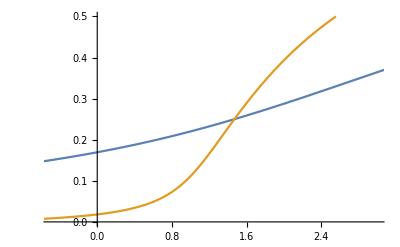

```mathematica
ListLinePlot[{datFastHigh[[;;,{3,1}]],datFastHigh[[;;,{2,1}]]},PlotRange->{{-.5,3},{0,.5}}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/RM_Fast_high.csv",datFastHigh]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/RM_Fast_high.csv

# (Upper Right) High Freq Travel; Low L2 PR

```mathematica
tarpars= {ϕ1->1/180., τ12 ->1/10.,ϕ2->1/180.,τ21 ->1/10.};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
PRpars={PR1->X,PR2->.05}; (*High transmission in location 2*)
```

```mathematica
RTaR[.04,.3]/.RMpars/.tarpars/.poppars
RFlux[.04,.3]/.RMpars/.fluxpars/.tarpars/.poppars
```

{0.359857,1.75913}

{-13.4268,4.52535}

```mathematica
datFastLow = Table[Flatten[{
X,
RTaR[X,PR2][[1]]/.PRpars/.RMpars/.tarpars/.poppars,
RFlux[X,PR2][[1]]/.PRpars/.RMpars/.fluxpars/.tarpars/.poppars}],
{X,0.001,.5,.001}];
```

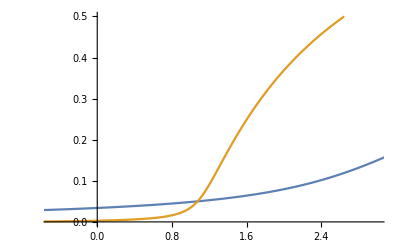

```mathematica
ListLinePlot[{datFastLow[[;;,{3,1}]],datFastLow[[;;,{2,1}]]},PlotRange->{{-.5,3},{0,.5}}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/RM_Fast_low.csv",datFastLow]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/RM_Fast_low.csv

# (Lower Left) Low Freq Travel; High L2 PR

```mathematica
1/180/400
```

1/72000

```mathematica
tarpars= {ϕ1->1/180/400., τ12 ->1/10/400,ϕ2->1/180./400,τ21 ->1/10/400};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
PRpars={PR1->X,PR2->.25}; (*High transmission in location 2*)
```

```mathematica
RTaR[.04,.3]/.RMpars/.tarpars/.poppars
RFlux[.04,.3]/.RMpars/.fluxpars/.tarpars/.poppars
```

{0.359857,1.75913}

{1.02233,1.60945}

```mathematica
datSlowHigh= Table[Flatten[{
X,
RTaR[X,PR2][[1]]/.PRpars/.RMpars/.tarpars/.poppars,
RFlux[X,PR2][[1]]/.PRpars/.RMpars/.fluxpars/.tarpars/.poppars}],
{X,0.001,.5,.001}];
```

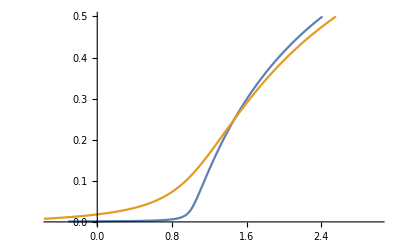

```mathematica
ListLinePlot[{datSlowHigh[[;;,{3,1}]],datSlowHigh[[;;,{2,1}]]},PlotRange->{{-.5,3},{0,.5}}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/RM_Slow_high.csv",datSlowHigh]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/RM_Slow_high.csv

# (Lower Right) High Freq Travel; Low L2 PR

```mathematica
tarpars= {ϕ1->1/180./400, τ12 ->1/10/400.,ϕ2->1/180./400,τ21 ->1/10/400};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
PRpars={PR1->X,PR2->.05}; (*High transmission in location 2*)
```

```mathematica
RTaR[.04,.3]/.RMpars/.tarpars/.poppars
RFlux[.04,.3]/.RMpars/.fluxpars/.tarpars/.poppars
```

{0.359857,1.75913}

{1.02233,1.60945}

```mathematica
datSlowLow = Table[Flatten[{
X,
RTaR[X,PR2][[1]]/.PRpars/.RMpars/.tarpars/.poppars,
RFlux[X,PR2][[1]]/.PRpars/.RMpars/.fluxpars/.tarpars/.poppars}],
{X,0.001,.5,.001}];
```

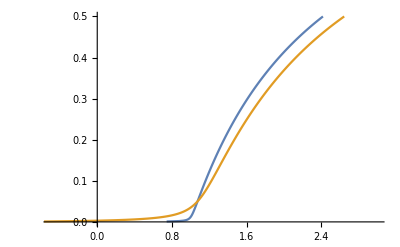

```mathematica
ListLinePlot[{datSlowLow[[;;,{3,1}]],datSlowLow[[;;,{2,1}]]},PlotRange->{{-.5,3},{0,.5}}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/RM_Slow_low.csv",datSlowLow]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/RM_Slow_low.csv